```mathematica
(*Import the data*)
```

```mathematica
data=Import["./Downloads/qmp4015final.csv","csv"];
```

```mathematica
(*for h4015*)
```

```mathematica
data1=Drop[Transpose[data],1];
```

```mathematica
(*Transpose data to select the top 15 species*)
```

```mathematica
total={};
Do[AppendTo[total,Total[Drop[data1[[n]],1]]],{n,2,Length[data1]}]
```

```mathematica
topx=15;
```

```mathematica
top15={};
Do[AppendTo[top15,data1[[Flatten[Position[total,TakeLargest[total,topx][[n]]]]+1]]],{n,1,topx}]
```

```mathematica
(*put all the information for plotting in one*)
```

```mathematica
all={};
AppendTo[all,Transpose[data][[1]]];Do[AppendTo[all,Flatten[top15[[n]]]],{n,1,topx}]
```

```mathematica
Length[top15]
```

15

```mathematica
Length[all]
```

16

```mathematica
(*add "other" for all the samples*)
```

```mathematica
repli2=Import["./Downloads/qpcr_after16srrna_normalization.csv","csv"];
```

```mathematica
repli2
```

{{name,cal},{HSM67VDR,0.920671},{HSM6XRUL,4.06912},{HSM6XRUN,24.8991},{HSM6XRUR,13.6711},{HSM6XRQ8,2.64966},{HSM7CZ16,8.93647},{HSM7CZ18,21.6134},{HSM7CZ1A,6.31226},{HSM7CZ1C,0.00171712},{HSM7CZ1E,1.21115},{HSM7CZ1G,3.1195},{HSM7J4HA,14.0211},{HSM7J4HC,26.9755},{HSM7J4HE,1.47025},{HSM7J4HG,32.8366},{HSM7J4HI,5.90012},{HSM7J4HK,4.31395},{HSM7J4KC,15.8756},{HSM7J4KG,0.560736},{HSM7J4KI,27.2007},{HSM7J4KK,1.93285},{HSM7J4KM,27.5508},{HSM5MD5X,7.40197},{HSM5MD62,67.0215},{HSM5MD6Y,50.6843},{HSM5MD71,25.3471},{HSM5MD73,4.56525},{HSM5MD75,0.496049},{HSM6XRS4,7.95642},{HSM6XRS6,13.4731},{HSM6XRS8,17.0505},{HSM6XRSE,26.5814},{HSM7CYZ5,29.1104},{HSM7CYZ7,0.0680027},{HSM7CYZ9,1.36009},{HSM7CYZB,4.24047},{HSM7CYZD,24.346},{HSM7CYZF,25.8196},{HSM7J4QB,26.1729},{HSM7J4QD,12.803},{HSM7J4QF,13.5572},{HSM7J4QH,2.29768×10^-6},{HSM7J4QJ,23.4715},{HSM7J4QL,15.7057}}

```mathematica
other={};
Do[AppendTo[other,repli2[[Flatten[Position[Transpose[repli2][[1]],Transpose[all][[n]][[1]]]]]][[1]][[2]]],{n,2,23}]
```

```mathematica
Position[Transpose[repli2][[1]],Transpose[all][[3]][[1]]]
```

{{25}}

```mathematica
repli2[[18]]
```

{HSM7J4HK,4.31395}

```mathematica
other={};
Do[AppendTo[other,repli2[[Flatten[Position[Transpose[repli2][[1]],Transpose[all][[n]][[1]]]]]][[1]][[2]]-Total[Drop[Transpose[all][[n]],1]]],{n,2,23}]
```

```mathematica
Transpose[all][[2]]
```

{HSM5MD5X,2.12346,0.263584,1.73829,0.0144427,0.374008,0.00136418,0.0518997,0.0869887,0.0311542,0.0394843,0.0373341,0.342957,0.100944,0.267507,0.300567}

```mathematica
other
```

{1.62798,15.9447,6.44202,3.72198,0.813564,0.065222,5.63273,2.24832,6.50777,4.09678,1.71681,0.0103409,0.126638,0.23699,0.880844,3.20966,2.70743,0.88113,0.635268,3.09154×10^-7,0.107647,1.2641}

```mathematica
all = Insert[all,Flatten[{"other",other}],2];
```

```mathematica
Length[all]
```

17

```mathematica
(*create the genus name for labeling*)
names=Drop[Transpose[all][[1]],1];
```

```mathematica
names1={};
AppendTo[names1,names[[1]]];
Do[AppendTo[names1,StringSplit[StringSplit[names[[n]],"|"][[7]],"__"][[2]]],{n,2,Length[names]}]
```

```mathematica
names1
```

{other,Faecalibacterium_prausnitzii,Bacteroides_fragilis,Bacteroides_vulgatus,Eubacterium_rectale,Sutterella_wadsworthensis,Peptostreptococcaceae_noname_unclassified,Roseburia_intestinalis,Bacteroides_caccae,Bacteroides_thetaiotaomicron,Haemophilus_parainfluenzae,Escherichia_coli,Bacteroides_ovatus,Subdoligranulum_unclassified,Bacteroides_xylanisolvens,Veillonella_unclassified}

```mathematica
StringSplit[StringSplit[names[[5]],"|"][[7]],"__"][[2]]
```

Eubacterium_rectale

```mathematica
StringSplit[names[[2]],"|"][[7]]
```

s__Faecalibacterium_prausnitzii

```mathematica
(*Plotting*)
```

```mathematica
data=Drop[Transpose[Drop[all,1]],1];
```

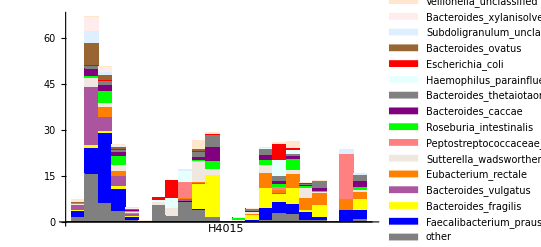

```mathematica
BarChart[data,ChartLabels->{{,,,,,,,,,,,"H4015",,,,,,,,,},None},
ChartLayout -> "Stacked",ChartStyle -> { Gray,Blue,Yellow,Blend[{Purple,LightYellow},1/3],Orange, LightBrown,Pink,Green, Purple, Gray,LightCyan,Red,Brown, LightBlue, LightPink,LightOrange},ChartLegends->names1,BaseStyle->{FontWeight->"Bold",FontSize->12},AxesStyle->Directive[Black,12]]
```